```mathematica
sf=Import["G:\\calc-online\\polarized\\spf\\numcalc\\spfnumre\\spf-kr-right-ξ1-L1.wdx"];
ft1=Query[1,1]@sf;
ft2=Query[2,1]@sf;
gt1=Query[1,2]@sf;
gt2=Query[2,2]@sf;
fp1=Interpolation[Flatten[ft1,1]];
```

```mathematica
sf2=Import["G:\\calc-online\\polarized\\spf\\numcalc\\spfnumre\\spf-kr-left-ξ1-L1.wdx"];
ft1l=Query[1,1]@sf2;

fp1l=Interpolation[Flatten[ft1l,1]];
```

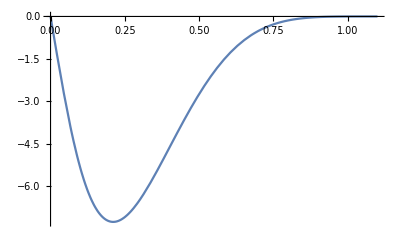

```mathematica
Plot[-I*fp1[x,-1],{x,0,1+0.1}]
```

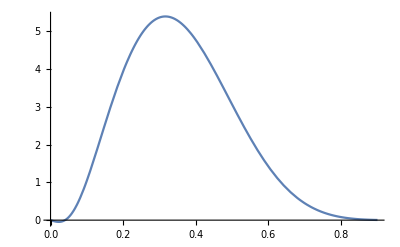

```mathematica
Plot[-I*fp1[x,-1],{x,0,0.9}]
```

InterpolatingFunction::dmval: Input value {1.1,-1} lies outside the range of data in the interpolating function. Extrapolation will be used.

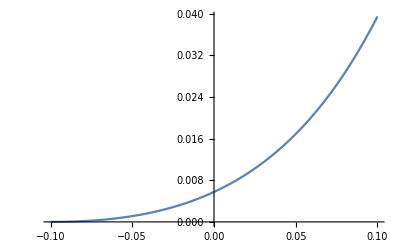

```mathematica
Plot[-I*fp2[1-x,-1],{x,-0.1,0.1}]
```

InterpolatingFunction::dmval: Input value {1.1,-1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.899982,-1} lies outside the range of data in the interpolating function. Extrapolation will be used.

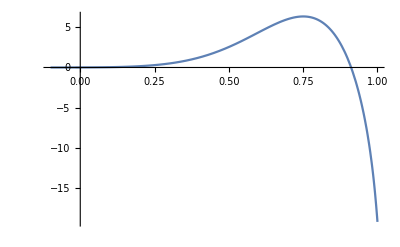

```mathematica
Show[Plot[-I*fp2[1-x,-1],{x,-0.1,0.1},PlotRange->All],Plot[-I*fp1[1-x,-1],{x,0.1,1},PlotRange->All]]
```

```mathematica
fp2[1,-1]
```

0.-0.000262237 ⅈ

InterpolatingFunction::dmval: Input value {0.900004,-1} lies outside the range of data in the interpolating function. Extrapolation will be used.

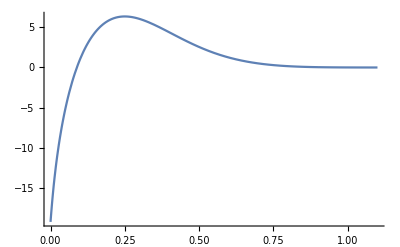

```mathematica
Show[Plot[-I*fp2[x,-1],{x,0.9,1.1},PlotRange->All],Plot[-I*fp1[x,-1],{x,0,0.9},PlotRange->All]]
```

InterpolatingFunction::dmval: Input value {1.1,-1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.899982,-1} lies outside the range of data in the interpolating function. Extrapolation will be used.

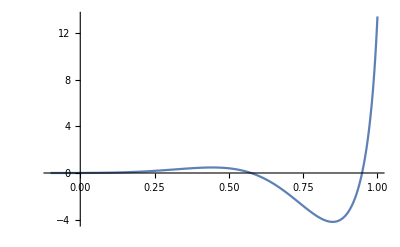

```mathematica
Show[Plot[-I*gp2[1-x,-1],{x,-0.1,0.1},PlotRange->All],Plot[-I*gp1[1-x,-1],{x,0.1,1},PlotRange->All]]
```

InterpolatingFunction::dmval: Input value {1.1,-1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.899982,-1} lies outside the range of data in the interpolating function. Extrapolation will be used.

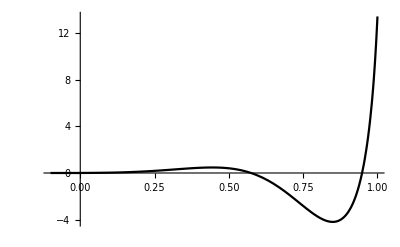
-Graphics-g_bȳξ=0.1

```mathematica
Labeled[Show[Plot[-I*gp2[1-x,-1],{x,-0.1,0.1},PlotRange->All,PlotStyle->{Black,Thick}],Plot[-I*gp1[1-x,-1],{x,0.1,1},PlotRange->All,PlotStyle->{Black,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[g,b],FontSlant->"Italic"]//DisplayForm,
StyleBox[OverscriptBox[y,_],FontSlant->"Italic"]//DisplayForm,"ξ=0.1"},{Left,Top,Right},LabelStyle->20]
```

```mathematica
StyleBox[OverscriptBox[y,_],FontSlant->"Italic"]//DisplayForm
```

ȳ

```mathematica
pathf=FileNameJoin[{"G:\\calc-online\\polarized\\spf\\pic","kr-right.pdf"}];
pathg=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"t-g-0.1-n.pdf"}];
```

```mathematica
Export[pathf,Labeled[Show[Plot[-I*fp1[1-x,-1],{x,-0.1,1},PlotStyle->{Black,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[f,e],FontSlant->"Italic"]//DisplayForm,
StyleBox[OverscriptBox[y,_],FontSlant->"Italic"]//DisplayForm,"ξ=0.1"},{Left,Top,Right},LabelStyle->20]]
```

G:\output\summary\gpd\pic\e-f-0.1-n.pdf

```mathematica
Export[pathf,Labeled[Show[Plot[-I*fp1[1-x,-1],{x,-0.1,1},PlotStyle->{Black,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[f,s],FontSlant->"Italic"]//DisplayForm,
StyleBox[OverscriptBox[y,_],FontSlant->"Italic"]//DisplayForm,"ξ=0.1"},{Left,Top,Right},LabelStyle->20]]
Export[pathg,Labeled[Show[Plot[-I*gp1[1-x,-1],{x,-0.1,1},PlotStyle->{Black,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[g,s],FontSlant->"Italic"]//DisplayForm,
StyleBox[OverscriptBox[y,_],FontSlant->"Italic"]//DisplayForm,"ξ=0.1"},{Left,Top,Right},LabelStyle->20]]
```

G:\output\summary\gpd\pic\s-f-0.1-n.pdf

G:\output\summary\gpd\pic\s-g-0.1-n.pdf

```mathematica
Export[pathf,Labeled[Show[Plot[-I*fp2[1-x,-1],{x,0.1,1},PlotRange->All,PlotStyle->{Black,Thick}],Plot[-I*fp1[1-x,-1],{x,1,1+0.2},PlotRange->All,PlotStyle->{Black,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[f,t],FontSlant->"Italic"]//DisplayForm,
StyleBox[OverscriptBox[y,_],FontSlant->"Italic"]//DisplayForm,"ξ=0.1"},{Left,Top,Right},LabelStyle->20]]
Export[pathg,Labeled[Show[Plot[-I*gp2[1-x,-1],{x,0.1,1},PlotRange->All,PlotStyle->{Black,Thick}],Plot[-I*gp1[1-x,-1],{x,1,1+0.2},PlotRange->All,PlotStyle->{Black,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[g,t],FontSlant->"Italic"]//DisplayForm,
StyleBox[OverscriptBox[y,_],FontSlant->"Italic"]//DisplayForm,"ξ=0.1"},{Left,Top,Right},LabelStyle->20]]
```

G:\output\summary\gpd\pic\t-f-0.1-n.pdf

G:\output\summary\gpd\pic\t-g-0.1-n.pdf

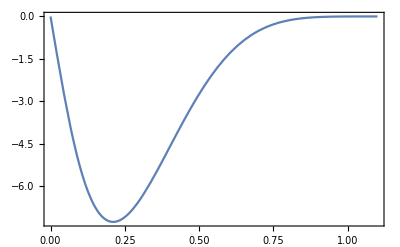
-Graphics-(f̃)_kryξ=0.1

```mathematica
picfr=Labeled[Show[Plot[-I*fp1[x,-1],{x,0,1.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{Subscript[f̃, kr],"y","ξ=0.1"},{Left,Bottom,Top},LabelStyle->24]
```

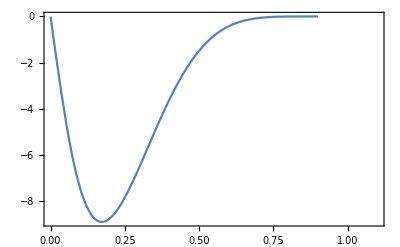
-Graphics-(f̃)_kryξ=0.1

```mathematica
picfl=Labeled[Show[Plot[-I*fp1l[x,-1],{x,0,0.9},PlotRange->{{0,1.1},All}],Frame->True,FrameStyle->Directive[Thick,20]],
{Subscript[f̃, kr],"y","ξ=0.1"},{Left,Bottom,Top},LabelStyle->24]
```

```mathematica
"\!\(\*TagBox[OverscriptBox[\"f\", \"~\"],DisplayForm]\)"
```

f̃

```mathematica
Subscript[OverscriptBox[f,"~"],kr]//DisplayForm
```

(f̃)_kr

```mathematica
pathfr=FileNameJoin[{"G:\\calc-online\\polarized\\spf\\pic","kr-right.pdf"}];
pathfl=FileNameJoin[{"G:\\calc-online\\polarized\\spf\\pic","kr-left.pdf"}];
```

```mathematica
Export[pathfr,picfr]
Export[pathfl,picfl]
```

G:\calc-online\polarized\spf\pic\kr-right.pdf

G:\calc-online\polarized\spf\pic\kr-left.pdf